### Analyzing the constitutive law for the wellbore

```mathematica
Clam=(π Di^4)/(128 μ);
Q1=Clam dpdx
Cturb=2.252610888 Di^(19/7)/(μ^(1/7)ρ^(3/7));
Q2=Cturb dpdx^(4/7)
```

```mathematica
(Di^4 dpdx π)/(128 μ)
```

(Di^4 dpdx π)/(128 μ)

#### Or, since Re = ρ V D/μ and V = (4Q)/(π D^2), then Re = (4 ρ Q)/(π D μ). Isolating Q we get Q = (π D μ Re)/(4 ρ)

{ρ→1000,μ→1/1000,Di→0.01}

0.032 R

0.0001582 R^(7/4)

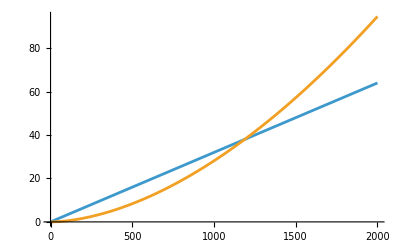

{{R→0.},{R→1187.38}}

```mathematica
cfg={ρ->1000,μ->10^-3,Di->0.01}
dpdx1=Q/Clam/.{Q->(π Di μ R)/(4 ρ)}/.cfg
dpdx2=(Q/Cturb)^(7/4)/.{Q->(π Di μ R)/(4 ρ)}/.cfg
Plot[{dpdx1,dpdx2},{R,0,2000}]

Solve[dpdx1==dpdx2,R]
```

### If we use the flow as velocity, then the curves do not match at Re = 1187.38

{ρ→1000,μ→1/1000,Di→0.01}

407.437 R

2414.34 R^(7/4)

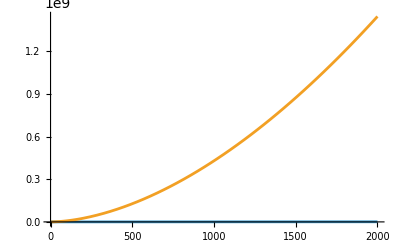

{{R→0.},{R→0.093257}}

```mathematica
cfg={ρ->1000,μ->10^-3,Di->0.01}
dpdx1=Q/Clam/.{Q->(R μ)/(ρ Di)}/.cfg
dpdx2=(Q/Cturb)^(7/4)/.{Q->(R μ)/(ρ Di)}/.cfg
Plot[{dpdx1,dpdx2},{R,0,2000}]
Solve[dpdx1==dpdx2,R]
```